# 2.1 Index of fixed point

```mathematica
a)
```

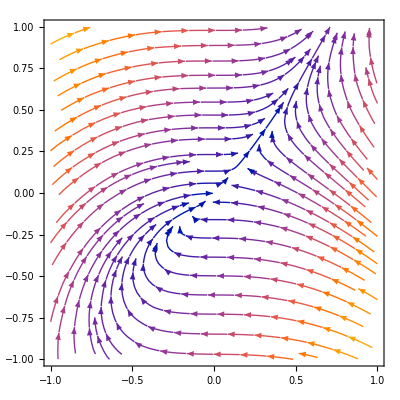

```mathematica
StreamPlot[{y-x, x^2}, {x,-1,1}, {y,-1,1}]
```

```mathematica
phi = ArcTan[x^2/(y-x)]
```

ArcTan[x^2/(-x+y)]

```mathematica
a = D[phi,x]//Simplify
```

-(x (x-2 y))/(x^2+x^4-2 x y+y^2)

```mathematica
b = D[phi,y]//Simplify
```

-x^2/(x^2+x^4-2 x y+y^2)

```mathematica
c = a/. x-> Cos[t]
```

-(Cos[t] (-2 y+Cos[t]))/(y^2-2 y Cos[t]+Cos[t]^2+Cos[t]^4)

```mathematica
c = c/. y->Sin[t]
```

-(Cos[t] (Cos[t]-2 Sin[t]))/(Cos[t]^2+Cos[t]^4-2 Cos[t] Sin[t]+Sin[t]^2)

```mathematica
d = b/. x-> Cos[t]
```

-Cos[t]^2/(y^2-2 y Cos[t]+Cos[t]^2+Cos[t]^4)

```mathematica
d =d/. y->Sin[t]
```

-Cos[t]^2/(Cos[t]^2+Cos[t]^4-2 Cos[t] Sin[t]+Sin[t]^2)

```mathematica
1/(2*π)*N[Integrate[c*-Sin[t]+d*Cos[t],{t,0,2*π}]]
```

0.+0. ⅈ

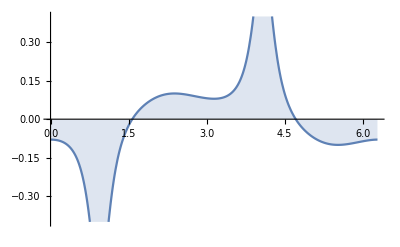

```mathematica
Plot[1/(2*π)*(c*-Sin[t]+d*Cos[t]),{t,0,2*π},Filling->Axis]
```

```mathematica
b)
```

```mathematica
theta = π/4
```

π/4

```mathematica
A = 1
```

1

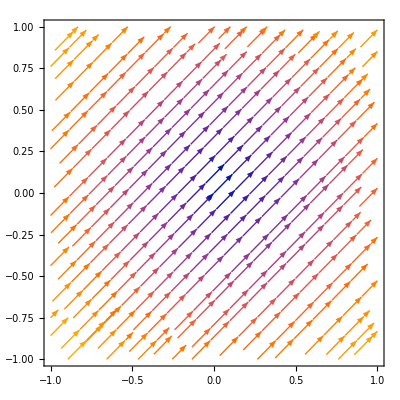

```mathematica
StreamPlot[{A*Sqrt[x^2+y^2]*Cos[theta], A*Sqrt[x^2+y^2]*Sin[theta]}, {x,-1,1}, {y,-1,1}]
```

```mathematica
phi = theta
```

π/4

Since dphi = 0, it follows that the index = 0

```mathematica
c)
```

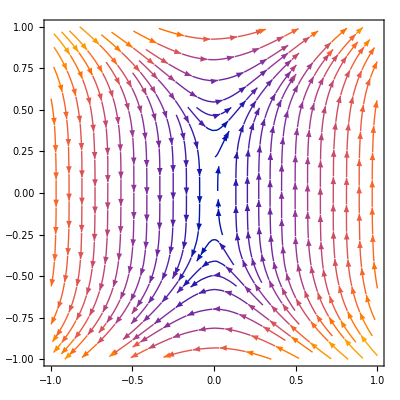

```mathematica
StreamPlot[{y^3, x}, {x,-1,1}, {y,-1,1}]
```

```mathematica
phi = ArcTan[x/y^3]
```

ArcTan[x/y^3]

```mathematica
a = D[phi,x]//Simplify
```

y^3/(x^2+y^6)

```mathematica
b = D[phi,y]//Simplify
```

-(3 x y^2)/(x^2+y^6)

```mathematica
c = a/. x-> Cos[t]
```

y^3/(y^6+Cos[t]^2)

```mathematica
c = c/. y->Sin[t]
```

Sin[t]^3/(Cos[t]^2+Sin[t]^6)

```mathematica
d = b/. x-> Cos[t]
```

-(3 y^2 Cos[t])/(y^6+Cos[t]^2)

```mathematica
d =d/. y->Sin[t]
```

-(3 Cos[t] Sin[t]^2)/(Cos[t]^2+Sin[t]^6)

```mathematica
1/(2*π)* N[Integrate[c*-Sin[t]+d*Cos[t],{t,0,2*π}]]
```

-1.-5.55112×10^-17 ⅈ

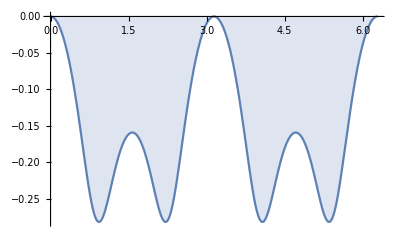

```mathematica
Plot[1/(2*π)*(c*-Sin[t]+d*Cos[t]),{t,0,2*π},Filling->Axis]
```

```mathematica
d)
```

```mathematica
m = 5
```

5

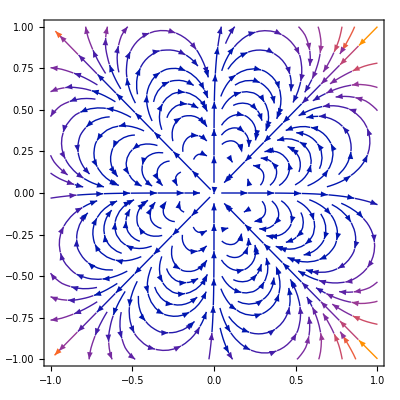

```mathematica
StreamPlot[{(x^2+y^2)^(m/2)*Cos[m*ArcTan[y/x]], (x^2+y^2)^(m/2)*Sin[m*ArcTan[y/x]]}, {x,-1,1}, {y,-1,1}]
```

```mathematica
phi = n*Arctan[y/x]
```

n Arctan[y/x]

```mathematica
a = D[phi,x]
```

-(n y Arctan'[y/x])/x^2

```mathematica
a = -n*y/(x^2+y^2)
```

-(n y)/(x^2+y^2)

```mathematica
b = D[phi,y]//Simplify
```

(n Arctan'[y/x])/x

```mathematica
b = n*x/(x^2+y^2)
```

(n x)/(x^2+y^2)

```mathematica
c = a/. x-> Cos[t]
```

-(n y)/(y^2+Cos[t]^2)

```mathematica
c = c/. y->Sin[t]//Simplify
```

-n Sin[t]

```mathematica
d = b/. x-> Cos[t]
```

(n Cos[t])/(y^2+Cos[t]^2)

```mathematica
d =d/. y->Sin[t]//Simplify
```

n Cos[t]

```mathematica
1/(2*π)* N[Integrate[c*-Sin[t]+d*Cos[t],{t,0,2*π}]]
```

1. n